Ideal MHD waves in a homogeneous plasma. Consider the following dimensionless parameters: Wavenumber k = 1, sound velocity v_s = 1, and angle that the wavevector forms with the equilibrium magnetic fi.0celd θ = π/4.

```mathematica
(By Lucas Romero Fernández)
```

Plot the solutions of the magnetoacoustic waves dispersion relation (ω = k v_A) for the Alfvén velocity v_A varying in the interval 0.1 < v_A < 10.

```mathematica
ωfast=Simplify[Sqrt[k^(2)/2 ((vA^(2)+vs^(2))+Sqrt[(vA^(2)+vs^(2))^(2)-4 vA^(2) vs^(2) (Cos[θ])^(2)])]] ;(*From the pdf files attached with this code*)
ωslow=Simplify[Sqrt[k^(2)/2 ((vA^(2)+vs^(2))-Sqrt[(vA^(2)+vs^(2))^(2)-4 vA^(2) vs^(2) (Cos[θ])^(2)])]] ;(*From the pdf files attached with this code*)
k=1;
vs=1;
θ=Pi/4;
ωfastlist={};
ωslowlist={};
vAlist=Range[0.1,10,0.1];
```

```mathematica
Do[AppendTo[ωfastlist,{Log10[vA],Simplify[ωfast] }];AppendTo[ωslowlist,{Log10[vA],Simplify[ωslow] }],{vA,vAlist}];
```

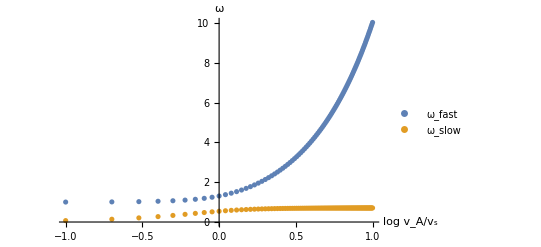

```mathematica
ListPlot[{ωfastlist,ωslowlist},AxesLabel->{"log v_A/v_s","ω"},PlotLegends->{"ω_fast","ω_slow"}]
```

Overplot the Alfvén wave frequency and the wave frequency of a pure acoustic (sound) wave.

```mathematica
vA=0.1; (*Pure acoustic (sound) wave (vA = 0, technically, but, for representation purposes, vA << vs = 1)*)
ωacousticlist={};
ωacoustic=Simplify[Sqrt[k^(2)/2 ((vA^(2)+vs^(2))+Sqrt[(vA^(2)+vs^(2))^(2)-4 vA^(2) vs^(2) (Cos[θ])^(2)])]] ;(*Constant for every Subscript[v, A]*)(*From the pdf files attached with this code*)
vs=0;(*Alfvén wave*)
ωAlfvenlist={};
ωfast=Simplify[Sqrt[k^(2)/2 ((vA^(2)+vs^(2))+Sqrt[(vA^(2)+vs^(2))^(2)-4 vA^(2) vs^(2) (Cos[θ])^(2)])]] ;(*From the pdf files attached with this code*)
```

```mathematica
Do[AppendTo[ωAlfvenlist,{Log10[vA],Simplify[ωfast]}];AppendTo[ωacousticlist,{Log10[vA],Simplify[ωacoustic]}],{vA,vAlist}];
```

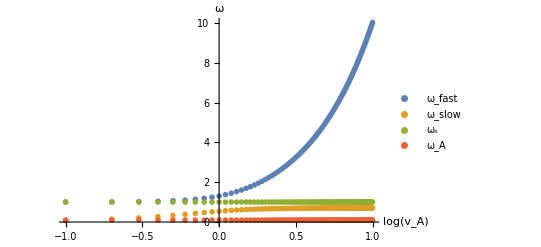

```mathematica
ListPlot[{ωfastlist,ωslowlist,ωacousticlist,ωAlfvenlist},AxesLabel->{"log(v_A)","ω"},PlotLegends->{"ω_fast","ω_slow","ω_s","ω_A"},PlotMarkers->{{●,3},{●,3},{●,7},{●,3}}]
```

Discuss the behavior of the slow and fast waves depending on the value of v_A compared to v_s and the angle θ. Explain what situation is most representative of the solar corona.

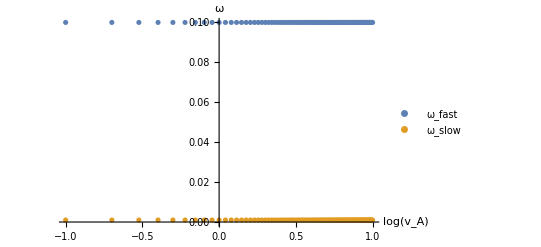

```mathematica
vs=0.001;(*small vs*) (*Situation most representative of the solar corona: vA>>vs*)
θ=0;(*Parallel to the magnetic field*)
ωfastlist2={};
ωslowlist2={};
Do[AppendTo[ωfastlist2,{Log10[vA],Simplify[ωfast] }];AppendTo[ωslowlist2,{Log10[vA],Simplify[ωslow] }],{vA,vAlist}];
ListPlot[{ωfastlist2,ωslowlist2},AxesLabel->{"log(v_A)","ω"},PlotLegends->{"ω_fast","ω_slow"}]
```

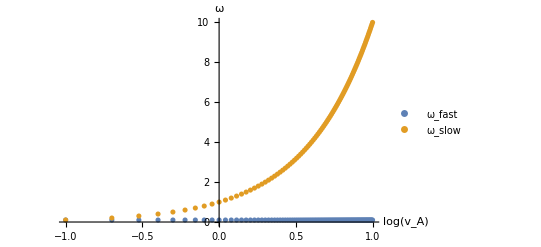

```mathematica
vs=100;(*big vs*)
θ=0;(*Parallel to the magnetic field*)
ωfastlist3={};
ωslowlist3={};
Do[AppendTo[ωfastlist3,{Log10[vA],Simplify[ωfast] }];AppendTo[ωslowlist3,{Log10[vA],Simplify[ωslow] }],{vA,vAlist}];
ListPlot[{ωfastlist3,ωslowlist3},AxesLabel->{"log(v_A)","ω"},PlotLegends->{"ω_fast","ω_slow"}]
```

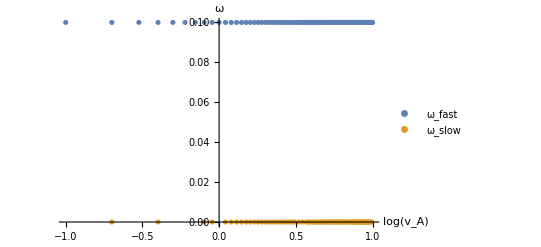

```mathematica
vs=0.001;(*small vs*)
θ=Pi/2;(*Perpendicular to the magnetic field*)
ωfastlist4={};
ωslowlist4={};
Do[AppendTo[ωfastlist4,{Log10[vA],Simplify[ωfast] }];AppendTo[ωslowlist4,{Log10[vA],Simplify[ωslow] }],{vA,vAlist}];
ListPlot[{ωfastlist4,ωslowlist4},AxesLabel->{"log(v_A)","ω"},PlotLegends->{"ω_fast","ω_slow"}]
```

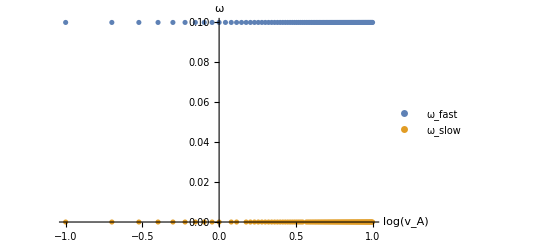

```mathematica
vs=100;(*big vs*)
θ=Pi/2;(*Perpendicular to the magnetic field*)
ωfastlist5={};
ωslowlist5={};
Do[AppendTo[ωfastlist5,{Log10[vA],Simplify[ωfast] }];AppendTo[ωslowlist5,{Log10[vA],Simplify[ωslow] }],{vA,vAlist}];
ListPlot[{ωfastlist5,ωslowlist5},AxesLabel->{"log(v_A)","ω"},PlotLegends->{"ω_fast","ω_slow"}]
```

The behavior shown coincides with the characteristics described within the pdf files attached.